```mathematica
(*Loads the GPT data, split into individual strings with ' ' delimeter*) 
SetDirectory[NotebookDirectory[]];
rawdata =Drop[Import["C:/Users/user/Documents/GPT_Code/EUV_Simple.txt","Words"],8];
(*remove bumf before this, first element is the 'time' then time then data*) 
(*19 columns of data*)(*Data of form: |data|time| 9e-9|data|*)
```

```mathematica
(*Get start index and time value of the data*)
timestamps=Array[f,{2,0}];
For[i=1,i<Length[rawdata],i++,
If[rawdata⟦i⟧=="time",
AppendTo[timestamps⟦1⟧,i];
AppendTo[timestamps⟦2⟧,rawdata⟦i+1⟧];
];
];
```

```mathematica
(*Delete the time data + the titles on the columns*)
shitdata=Partition[Join[timestamps⟦1⟧,(timestamps⟦1⟧+1),(timestamps⟦1⟧+2),(timestamps⟦1⟧+3),(timestamps⟦1⟧+4),(timestamps⟦1⟧+5),(timestamps⟦1⟧+6),(timestamps⟦1⟧+7),(timestamps⟦1⟧+8),(timestamps⟦1⟧+9),(timestamps⟦1⟧+10),(timestamps⟦1⟧+11),(timestamps⟦1⟧+12),(timestamps⟦1⟧+13),(timestamps⟦1⟧+14),(timestamps⟦1⟧+15),(timestamps⟦1⟧+16),(timestamps⟦1⟧+17),(timestamps⟦1⟧+18),(timestamps⟦1⟧+19),(timestamps⟦1⟧+20)],1];
data=Delete[rawdata,shitdata];
```

```mathematica
(*Creation of data array*)
noGPT=19;
(*no. outputs in GPT ASCII file*) 
nmeas=Length[timestamps⟦1⟧];
(*data took at 11 points*)
ndata=Length[data]/nmeas;
(*no. total data points for one measurement*)
npart=ndata/noGPT;
(*no. particles - 19 different types of data returned*)
xydata=Array[g,{3,nmeas,npart}];
(*measurement number to look at*)
(*α=2;*)
```

```mathematica
(*Filling Array*)
(*Problem with first point xydata⟦1,1⟧ not evaluating correctly unless ran twice*)
For[α=1,α<(nmeas+1),α++,
For[i=1,i<(npart+1),i++,
(*for x*)
g[1,α,i]=Interpreter["Number"][ToString[data⟦1+(ndata*(α-1))+(i-1)*noGPT⟧]];
(*for y*)
g[2,α,i]=Interpreter["Number"][ToString[data⟦2+(ndata*(α-1))+(i-1)*noGPT⟧]];
(*for z*)
g[3,α,i]=Interpreter["Number"][ToString[data⟦3+(ndata*(α-1))+(i-1)*noGPT⟧]];
];
];
(*Interpreter converts from 1e-7 form to proper number*)
```

```mathematica
xydata⟦1,5,1⟧
xydata⟦3,5,1⟧
```

6.0197×10^-7

0.00358935

```mathematica
timestamps⟦2,5⟧
```

1.200000000e-11

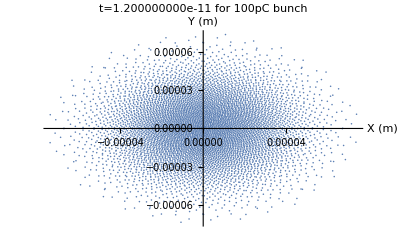
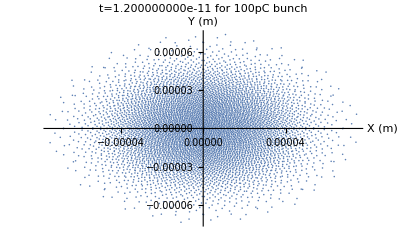
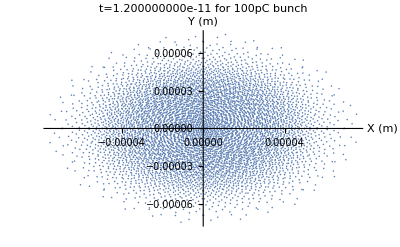
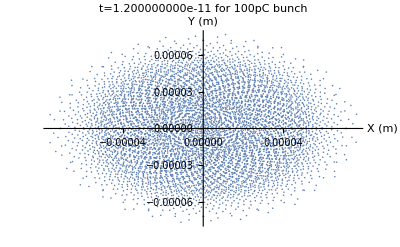
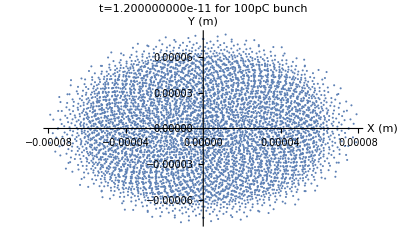
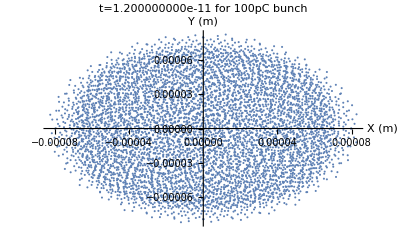
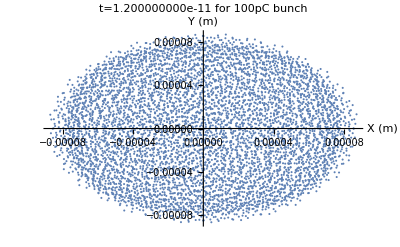
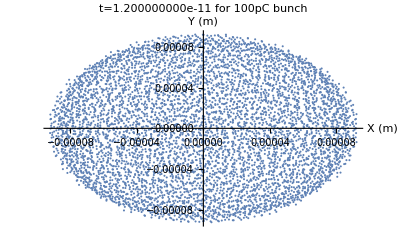

```mathematica
(*Plotting x-y*)
Table[ListPlot[Partition[Riffle[xydata⟦1,n,All⟧,xydata⟦2,n,All⟧],2],PlotRange->All,AxesLabel->{"X (m)","Y (m)"},PlotLabel->StringForm["t=`` for 100pC bunch",timestamps⟦2,5⟧]],{n,nmeas}]
```

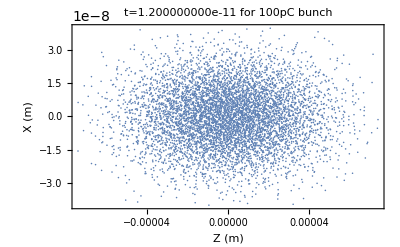
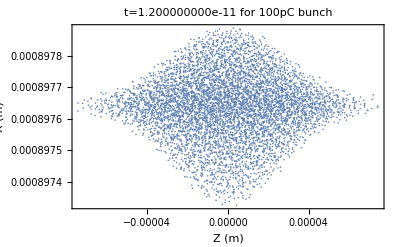
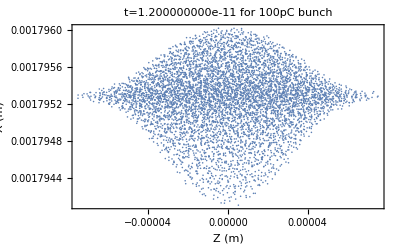
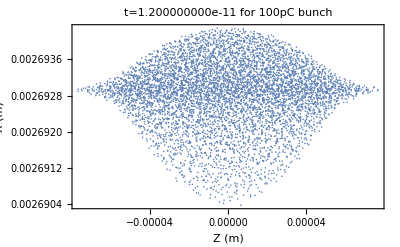
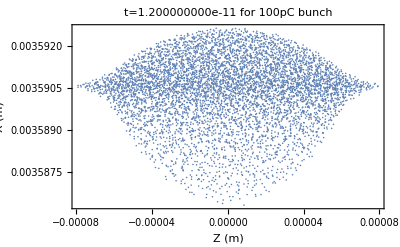
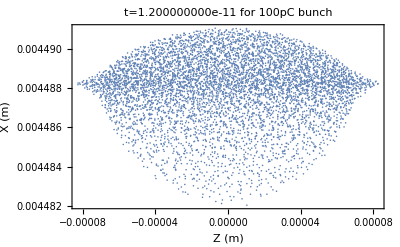
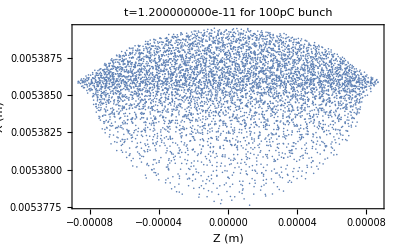
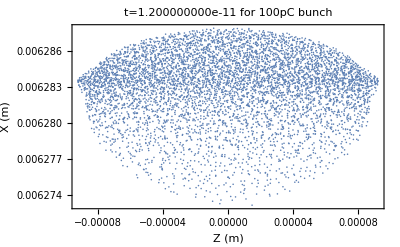

```mathematica
(*Plotting x-z*)
Table[ListPlot[Partition[Riffle[xydata⟦1,n,All⟧,xydata⟦3,n,All⟧],2],PlotRange->All,AxesLabel->{"Z (m)","X (m)"},PlotRange->{{-6*10^-5,6*10^-5},{-5*10^-8,5*10^-8}},PlotRangeClipping->True,Frame->True,PlotLabel->StringForm["t=`` for 100pC bunch",timestamps⟦2,5⟧]],{n,nmeas}]
```

```mathematica
(*Animation of this*)
Animate[ListPlot[Partition[Riffle[xydata⟦1,n,All⟧,xydata⟦3,n,All⟧],2],PlotRange->All,AxesLabel->{"Z (m)","X (m)"},PlotRange->{{-6*10^-5,6*10^-5},{-5*10^-8,5*10^-8}},PlotRangeClipping->True,Frame->True,PlotLabel->StringForm["t=`` for 100pC bunch",timestamps⟦2,5⟧]],{n,1,nmeas},AnimationRunning->False]
```